```mathematica
Quit[];
```

## Problem 2: Fisher information of 5 coin flips

Likelihood of each outcome

The coefficient in front of each expression arises from the number of ways to achieve that outcome (for example, there are 10 ways to have 3 heads and 2 tails). These coefficients come from a binomial distribution.

```mathematica
L[n_,h_]:=Binomial[n,h] (θ^h) (1-θ)^(n-h);
Lθ={{L[5,5]},{L[5,4]},{L[5,3]},{L[5,2]},{L[5,1]},{L[5,0]}};
```

Log-likelihood

```mathematica
lθ=Log[Lθ];
```

2nd derivative of log-likelihood

```mathematica
D2θlθ=D[D[lθ,θ],θ];
```

Fisher information

Fisher information (5 flips): I[θ] = 5/(θ-θ^2)

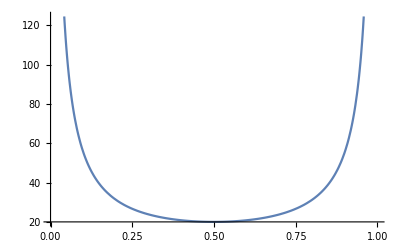

```mathematica
Iθ5=FullSimplify[-D2θlθᵀ.Lθ][[1,1]];
Print["Fisher information (5 flips): I[θ] = ",Iθ5];
Plot[Iθ5,{θ,0,1}]
```

Check against the 2-flip case

Fisher information (2 flips): I[θ] = 2/(θ-θ^2)

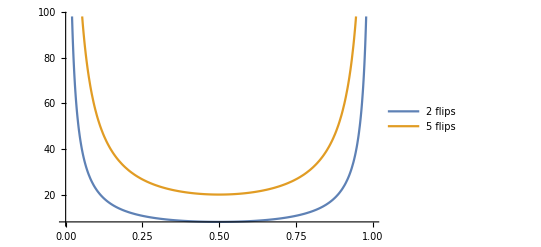

```mathematica
L2H=1 θ^2;
L1H1T=2 θ (1-θ);
L2T=1 (1-θ)^2;
Lθ2={{L2H},{L1H1T},{L2T}};

lθ2=Log[Lθ2];

D2θlθ2=D[D[lθ2,θ],θ];

Iθ2=FullSimplify[-D2θlθ2ᵀ.Lθ2][[1,1]];
Print["Fisher information (2 flips): I[θ] = ",Iθ2]
Plot[{Iθ2,Iθ5},{θ,0,1},PlotLegends->{"2 flips","5 flips"}]
```